```mathematica
h:=1/2(k11 Jx^(3/2) Sqrt[Jy]+k12 Sqrt[Jx] Jy^(3/2))(f11 Sin[ϕx-ϕy+2η π s]+Cos[ϕx-ϕy+2η π s])+3/8(p Jx^2+r Jy^2+2 q Jx Jy)-3/4f2 Jx Jy (f21 Sin[2ϕx-2ϕy+4η π s]+Cos[2ϕx-2ϕy+4η π s])+k1 Cos[ϕx+2 π s(νx+νy+η)/2-wr s]Sqrt[Jx]+k2 Cos[ϕy+2 π s(νx+νy-η)/2-wr s]Sqrt[Jy]
ϕxstr=D[h,Jx];
Jxstr=-D[h,ϕx];
ϕystr=D[h,Jy];
Jystr=-D[h,ϕy];
Jxstrd=Jxstr/.{Jx->Jx[t],Jy->Jy[t],ϕx->ϕx[t],ϕy->ϕy[t]};
Jystrd=Jystr/.{Jx->Jx[t],Jy->Jy[t],ϕx->ϕx[t],ϕy->ϕy[t]};
ϕxstrd=ϕxstr/.{Jx->Jx[t],Jy->Jy[t],ϕx->ϕx[t],ϕy->ϕy[t]};
ϕystrd=ϕystr/.{Jx->Jx[t],Jy->Jy[t],ϕx->ϕx[t],ϕy->ϕy[t]};
```

```mathematica
inputpr=({Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==Jxv,Jy[0]==Jyv,ϕx[0]==ϕxv,ϕy[0]==ϕyv}/.{f2->f2,R->1,p->p,r->r,q->q,η->δ,s->t, k1->k1,k2->k2,νx->0.185,νy->0.175,wr->wr,f21->0,f11->0,k11->.01,k12->0.01,n->t});
```

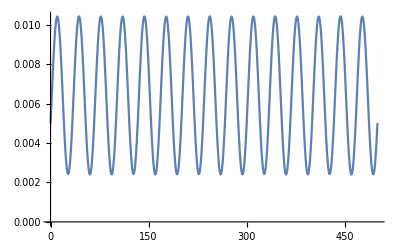

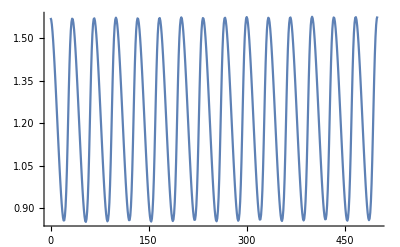

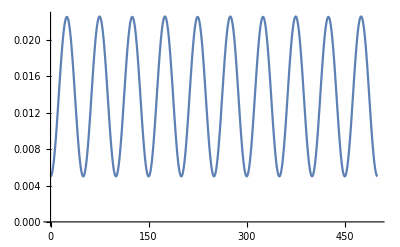

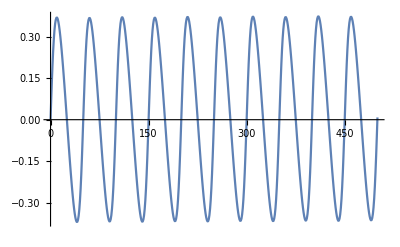

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->.01-Jxv1,ϕxv->π/2,ϕyv->0,f2->0.01,R->1,p->0,r->0,q->0,δ->0.01, k1->0.01,k2->0.01,νx->0.185,νy->0.175,wr->0.155 2π};
locsol=Flatten[NDSolve[inloc/.{Jxv1->.005},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]];
ListPlot[Table[{t1,(Jx[t]/.locsol)/.{t->t1}},{t1,0,500,1}],Joined->True]
ListPlot[Table[{t1,(ϕx[t]/.locsol)/.{t->t1}},{t1,0,500,1}],Joined->True]
ListPlot[Table[{t1,(Jy[t]/.locsol)/.{t->t1}},{t1,0,500,1}],Joined->True]
ListPlot[Table[{t1,(ϕy[t]/.locsol)/.{t->t1}},{t1,0,500,1}],Joined->True]
```

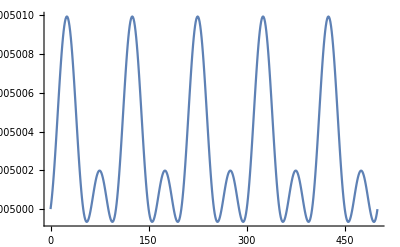

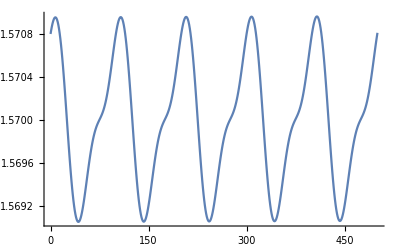

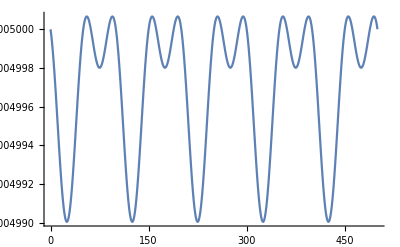

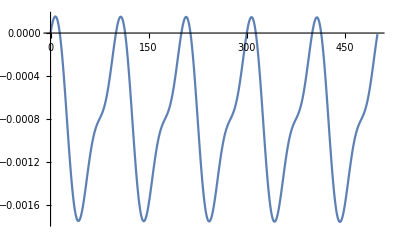

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->.01-Jxv1,ϕxv->π/2,ϕyv->0,f2->0.01,R->1,p->0,r->0,q->0,δ->0.01, k1->0.0,k2->0,νx->0.18,νy->0.18,wr->0.155 2π};
locsol=Flatten[NDSolve[inloc/.{Jxv1->.005},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]];
ListPlot[Table[{t1,(Jx[t]/.locsol)/.{t->t1}},{t1,0,500,1}],Joined->True]
ListPlot[Table[{t1,(ϕx[t]/.locsol)/.{t->t1}},{t1,0,500,1}],Joined->True]
ListPlot[Table[{t1,(Jy[t]/.locsol)/.{t->t1}},{t1,0,500,1}],Joined->True]
ListPlot[Table[{t1,(ϕy[t]/.locsol)/.{t->t1}},{t1,0,500,1}],Joined->True]
```

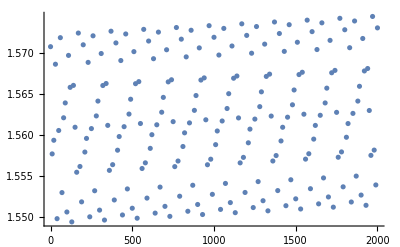
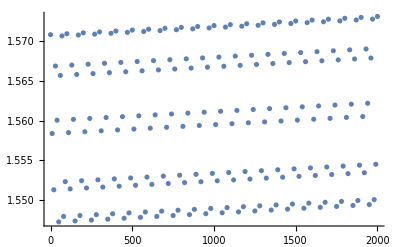
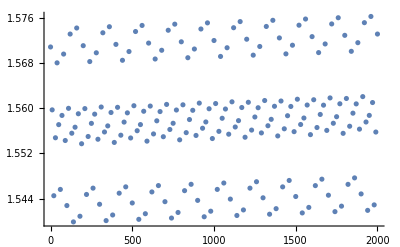
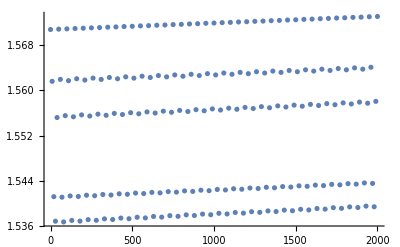
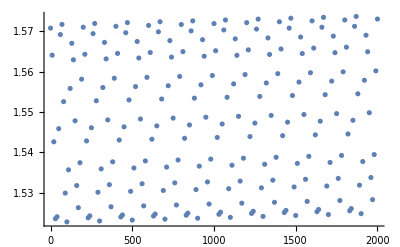
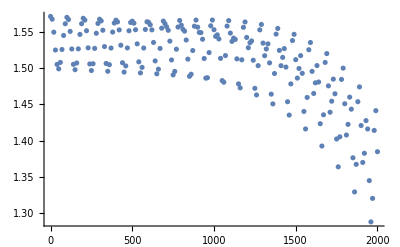
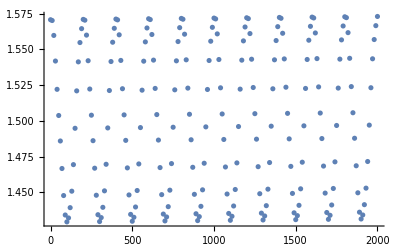

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->.1-Jxv1,ϕxv->π/2,ϕyv->0,f2->0.01,R->1,p->0,r->0,q->0,δ->0.01, k1->0.001,k2->0.001,νx->0.18,νy->0.18,wr->wr};
Table[ListPlot[Table[{t1,(ϕx[t]/.Flatten[NDSolve[inloc/.{Jxv1->.05},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,2000}]])/.{t->t1}},{t1,0,2000,10}]],{wr,0.15 2 π,0.18 2 π,0.005 2 π}]
```

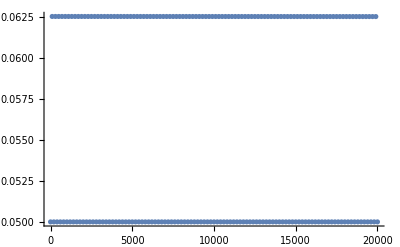
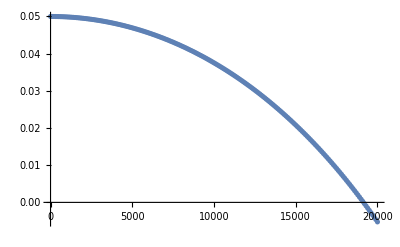
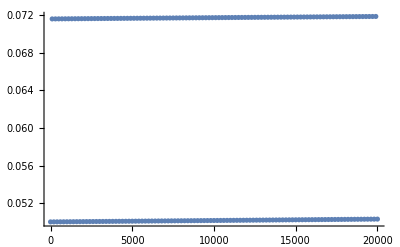
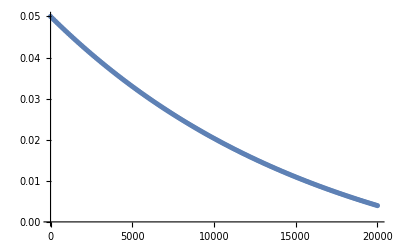
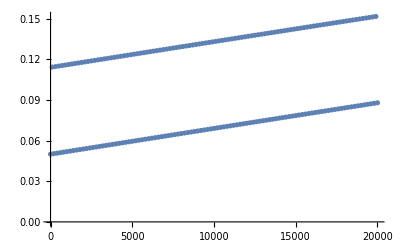
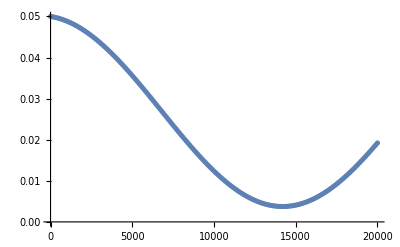
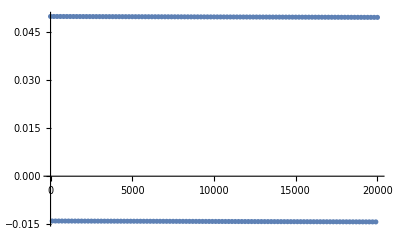

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->.1-Jxv1,ϕxv->π/2,ϕyv->0,f2->0.01,R->1,p->0,r->0,q->0,δ->0.01, k1->0.001,k2->0.001,νx->0.18,νy->0.18,wr->wr};
Table[ListPlot[Table[{t1,(Jy[t]/.Flatten[NDSolve[inloc/.{Jxv1->.05},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,20000}]])/.{t->t1}},{t1,0,20000,100}]],{wr,0.15 2 π,0.18 2 π,0.005 2 π}]
```

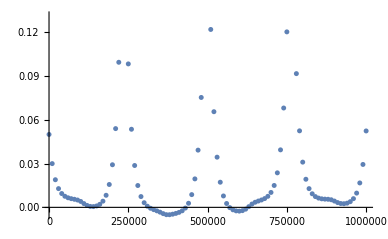

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->.1-Jxv1,ϕxv->π/2,ϕyv->0,f2->0.01,R->1,p->0,r->0,q->0,δ->0.01, k1->0.001,k2->0.001,νx->0.18,νy->0.18,wr->wr};
Table[ListPlot[Table[{t1,(Jy[t]/.Flatten[NDSolve[inloc/.{Jxv1->.05},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,1000000}]])/.{t->t1}},{t1,0,1000000,10000}]],{wr,0.205 2 π,0.205 2 π,0.005 2 π}]
```

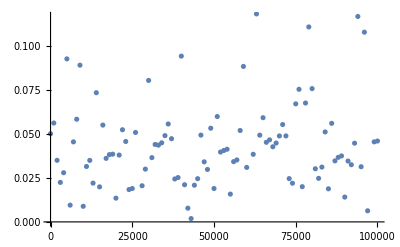

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->.1-Jxv1,ϕxv->π/2,ϕyv->0,f2->0.01,R->1,p->0,r->0,q->0,δ->0.01, k1->0.001,k2->0.001,νx->0.18,νy->0.18,wr->wr};
Table[ListPlot[Table[{t1,(Jy[t]/.Flatten[NDSolve[inloc/.{Jxv1->.05},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,100000}]])/.{t->t1}},{t1,0,100000,1000}]],{wr,0.185 2 π,0.185 2 π,0.005 2 π}]
```

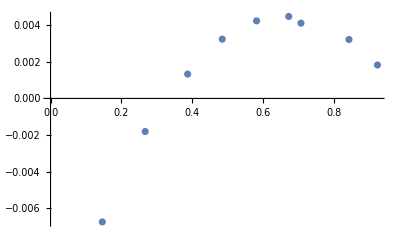

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.1,f2v->.1,pv->.0,rv->0,f1v->0,k11->0,k12->0,f11->0,f21->0,q->0};
ListPlot[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->t1})],{t1,0,5000,500}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->5000})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->0})))/5000},{Jxv1,0.1,0.9,.1}]]
```

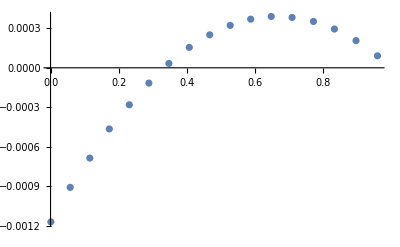

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.3,f2v->-.05,pv->.0,rv->0,f1v->0,k11->0,k12->0,f11->0,f21->0,q->0};
cplot=ListPlot[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->t1})],{t1,0,5000,500}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->5000})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->0})))/5000},{Jxv1,0.001,0.999,.06}]]
```

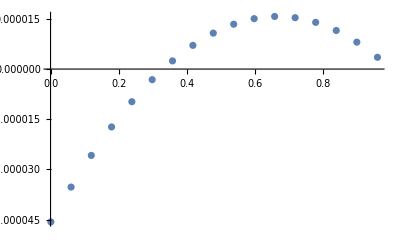

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.3,f2v->-.01,pv->.0,rv->0,f1v->0,k11->0,k12->0,f11->0,f21->0,q->0};
c1plot=ListPlot[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->t1})],{t1,0,5000,500}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->5000})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->0})))/5000},{Jxv1,0.001,0.999,.06}]]
```

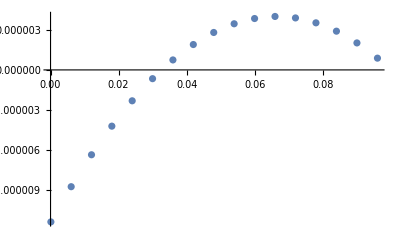

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->.1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.3,f2v->-.05,pv->.0,rv->0,f1v->0,k11->0,k12->0,f11->0,f21->0,q->0};
c2plot=ListPlot[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->t1})],{t1,0,5000,500}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->5000})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->0})))/5000},{Jxv1,0.0001,0.0999,.006}]]
```

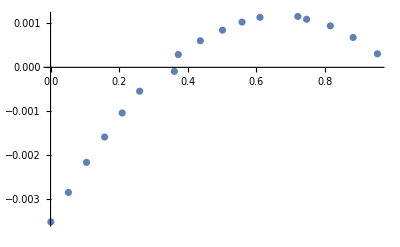

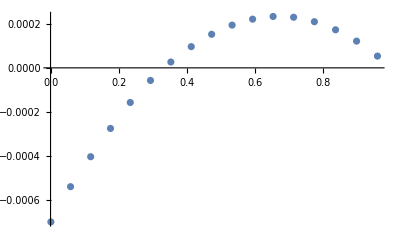

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.1,f2v->-.05,pv->.0,rv->0,f1v->0,k11->0,k12->0,f11->0,f21->0,q->0};
c3plot=ListPlot[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->t1})],{t1,0,5000,500}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->5000})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->0})))/5000},{Jxv1,0.001,0.999,.06}]]
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.5,f2v->-.05,pv->.0,rv->0,f1v->0,k11->0,k12->0,f11->0,f21->0,q->0};
c4plot=ListPlot[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->t1})],{t1,0,5000,500}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->5000})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->0})))/5000},{Jxv1,0.001,0.999,.06}]]
```

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->II-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.1,f2v->.1,pv->.0,rv->0,f1v->0,k11->0,k12->0,f11->0,f21->0,q->0};
Max[Table[(((ϕx[t]/.Flatten[NDSolve[inloc/.{II->.1},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->5000})-(((ϕx[t]/.Flatten[NDSolve[inloc/.{II->.1},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->0})))/5000,{Jxv1,0.01,0.09,.01}]]
Max[Table[(((ϕx[t]/.Flatten[NDSolve[inloc/.{II->.2},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->5000})-(((ϕx[t]/.Flatten[NDSolve[inloc/.{II->.2},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->0})))/5000,{Jxv1,0.02,0.18,.02}]]
Max[Table[(((ϕx[t]/.Flatten[NDSolve[inloc/.{II->.3},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->5000})-(((ϕx[t]/.Flatten[NDSolve[inloc/.{II->.3},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->0})))/5000,{Jxv1,0.03,0.27,.03}]]
Max[Table[(((ϕx[t]/.Flatten[NDSolve[inloc/.{II->.4},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->5000})-(((ϕx[t]/.Flatten[NDSolve[inloc/.{II->.4},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->0})))/5000,{Jxv1,0.04,0.36,.04}]]
Max[Table[(((ϕx[t]/.Flatten[NDSolve[inloc/.{II->.5},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->5000})-(((ϕx[t]/.Flatten[NDSolve[inloc/.{II->.5},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->0})))/5000,{Jxv1,0.05,0.45,.05}]]
```

0.0000469691

0.000183112

0.00041696

0.000732703

0.00115699

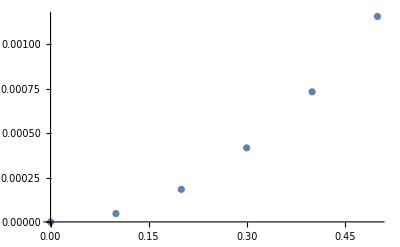

```mathematica
aplot=ListPlot[{{0,0},{.1,0.0000469691210346479},{.2,0.00018311155137783235},{.3,0.0004169596507615248},{.4,0.00073270347381369},{.5,0.0011569928431083203}}]
```

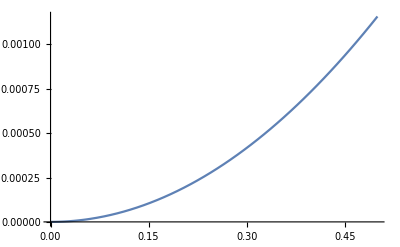

```mathematica
bplot=Plot[0.00463x^2,{x,0,0.5}]
```

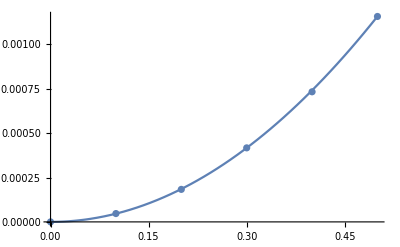

```mathematica
Show[{aplot,bplot}]
```

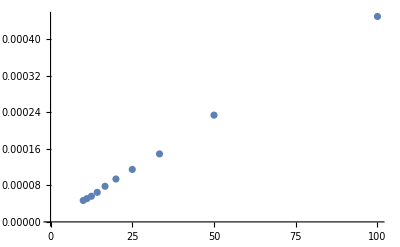

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->δv,f2v->.01,pv->.0,rv->0,f1v->0,k11->0,k12->0,f11->0,f21->0,q->0};
ListPlot[Table[{1/δv,Max[Table[(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->5000})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->0})))/5000,{Jxv1,0.1,0.9,.1}]]},{δv,0.01,.1,0.01}]]
```

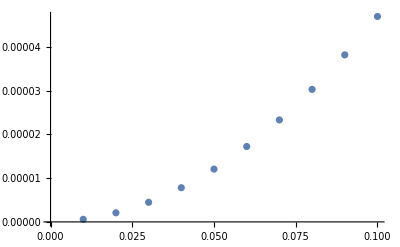

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->.1-Jxv1,ϕxv->π/2,ϕyv->0,δv->.1,f2v->f2v,pv->.0,rv->0,f1v->0,k11->0,k12->0,f11->0,f21->0,q->0};
f2plot=ListPlot[Table[{f2v,Max[Table[(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->5000})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->0})))/5000,{Jxv1,0.01,0.09,.01}]]},{f2v,0.01,0.1,0.01}]]
```

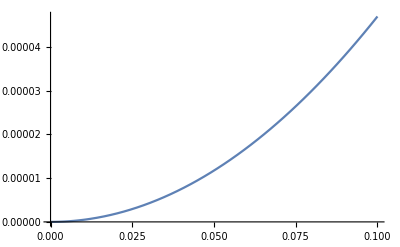

```mathematica
bf2plot=Plot[0.0047x^2,{x,0,0.1}]
```

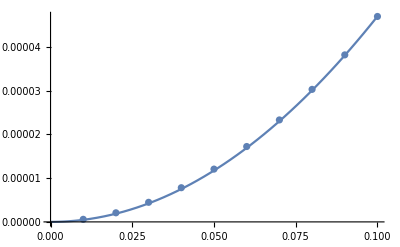

```mathematica
Show[{f2plot,bf2plot}]
```

```mathematica
8.2 0.0463
```

0.37966

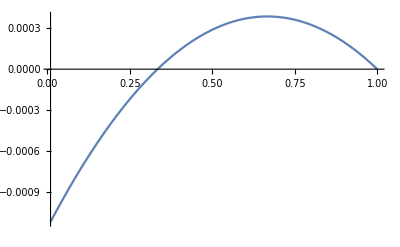

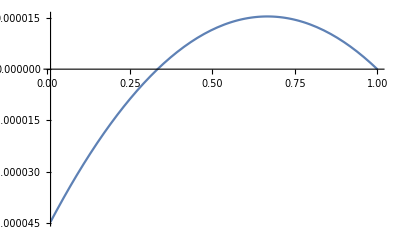

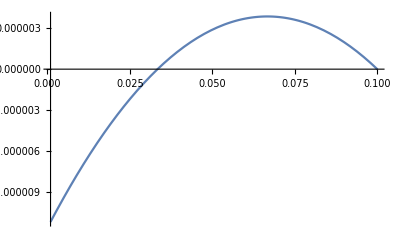

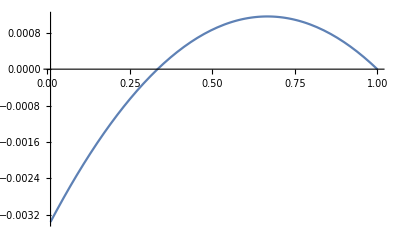

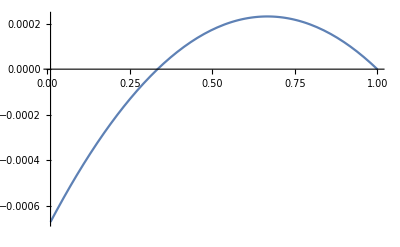

```mathematica
dplot=Plot[0.0463 1 0.0025/0.3 (-8.2(2.1x-1.4)^2+4)0.25,{x,0.01,1}]
d1plot=Plot[0.0463 1 0.0001/0.3 (-8.2(2.1x-1.4)^2+4)0.25,{x,0.01,1}]
d2plot=Plot[0.0463 1 0.0025/0.3 (-8.2(2.1x-.14)^2+4 0.01)0.25,{x,0.001,.1}]
d3plot=Plot[0.0463 1 0.0025/0.1 (-8.2(2.1x-1.4)^2+4)0.25,{x,0.01,1}]
d4plot=Plot[0.0463 1 0.0025/0.5 (-8.2(2.1x-1.4)^2+4)0.25,{x,0.01,1}]
```

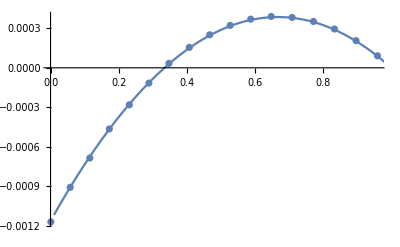

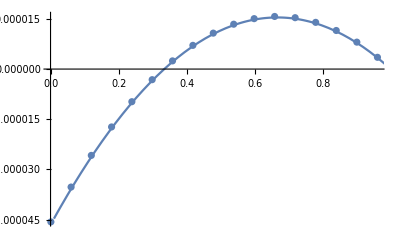

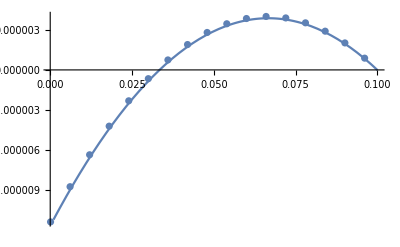

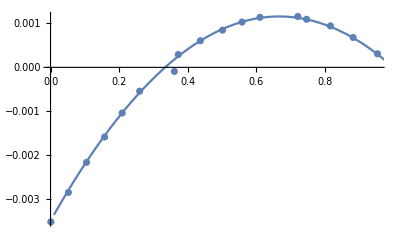

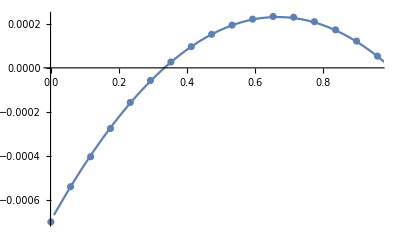

```mathematica
Show[{cplot,dplot}]
Show[{c1plot,d1plot}]
Show[{c2plot,d2plot},PlotRange->All]
Show[{c3plot,d3plot}]
Show[{c4plot,d4plot}]
```

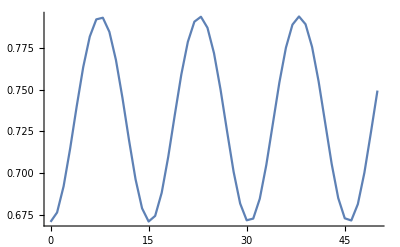

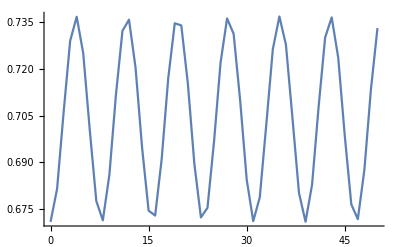

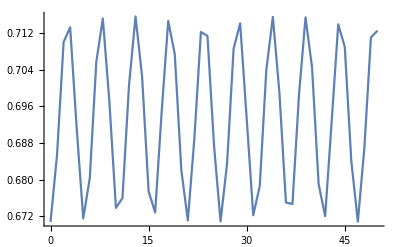

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.1,f2v->.1,pv->.0,rv->0,f1v->0,k11->0,k12->0,f11->0,f21->0,q->0};
locsol=Flatten[NDSolve[inloc/.{Jxv1->.45},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50000}]];
ListPlot[Table[{t1,(Sqrt[Jx[t]/.locsol])/.{t->t1}},{t1,0,50,1}],Joined->True]
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.2,f2v->.1,pv->.0,rv->0,f1v->0,k11->0,k12->0,f11->0,f21->0,q->0};
locsol=Flatten[NDSolve[inloc/.{Jxv1->.45},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50000}]];
ListPlot[Table[{t1,(Sqrt[Jx[t]/.locsol])/.{t->t1}},{t1,0,50,1}],Joined->True]
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.3,f2v->.1,pv->.0,rv->0,f1v->0,k11->0,k12->0,f11->0,f21->0,q->0};
locsol=Flatten[NDSolve[inloc/.{Jxv1->.45},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50000}]];
ListPlot[Table[{t1,(Sqrt[Jx[t]/.locsol])/.{t->t1}},{t1,0,50,1}],Joined->True]
```

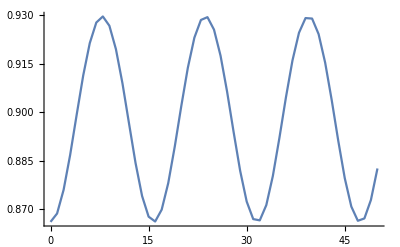

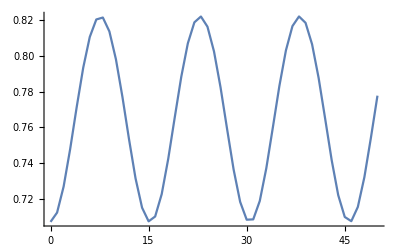

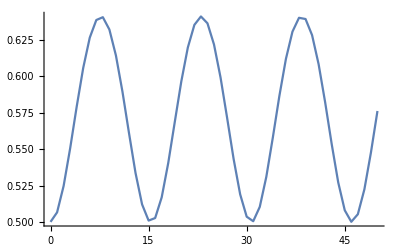

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.1,f2v->.1,pv->.0,rv->0,f1v->0,k11->0,k12->0,f11->0,f21->0,q->0};
locsol=Flatten[NDSolve[inloc/.{Jxv1->.75},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50000}]];
ListPlot[Table[{t1,(Sqrt[Jx[t]/.locsol])/.{t->t1}},{t1,0,50,1}],Joined->True]
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.1,f2v->.1,pv->.0,rv->0,f1v->0,k11->0,k12->0,f11->0,f21->0,q->0};
locsol=Flatten[NDSolve[inloc/.{Jxv1->.5},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50000}]];
ListPlot[Table[{t1,(Sqrt[Jx[t]/.locsol])/.{t->t1}},{t1,0,50,1}],Joined->True]
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.1,f2v->.1,pv->.0,rv->0,f1v->0,k11->0,k12->0,f11->0,f21->0,q->0};
locsol=Flatten[NDSolve[inloc/.{Jxv1->.25},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50000}]];
ListPlot[Table[{t1,(Sqrt[Jx[t]/.locsol])/.{t->t1}},{t1,0,50,1}],Joined->True]
```

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.1,f2v->.1,pv->.0001,rv->.0001,f1v->0,k11->.00001,k12->.0001,f11->.0001,f21->.0001,q->.0001};
Fit[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,50}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->500})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->0})))/500},{Jxv1,0.1,0.9,.1}],{1,x},x]
```

-0.00407669+0.0101489 x

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->.5-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.1,f2v->0.01,pv->.0,rv->.1,f1v->0,k11->.05,k12->-.05};
Fit[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,50}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->500})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->0})))/500},{Jxv1,0.1,0.4,.05}],{1,x},x]
```

-0.00745662+0.0148423 x

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->.3-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.1,f2v->0.01,pv->.0,rv->.1,f1v->0,k11->.05,k12->-.05};
Fit[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,50}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->500})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->0})))/500},{Jxv1,0.05,0.25,.025}],{1,x},x]
```

-0.00449395+0.0149731 x

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->.1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.1,f2v->0.01,pv->.0,rv->.1,f1v->0,k11->.05,k12->-.05};
Fit[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,50}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->500})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->0})))/500},{Jxv1,0.01,0.09,.01}],{1,x},x]
```

-0.00150189+0.015031 x

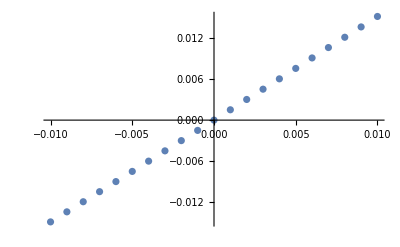

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->.1,f2v->f2v,pv->0,rv->0,k11->0,k12->0};
ListPlot[Table[{f2v,(1/x Fit[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,50}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->500})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->0})))/500},{Jxv1,0.1,0.9,.1}],{1,x},x])/.{x->10000}},{f2v,-.01,.01,0.001}]]
```

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.1,f2v->0,pv->f2v,rv->0,k11->0,k12->0};
Fit[Table[{f2v,(1/x Fit[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,50}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->500})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->0})))/500},{Jxv1,0.1,0.9,.1}],{1,x},x])/.{x->10000}},{f2v,-1,1,0.1}],{1,x},x]
```

2.85807×10^-17+0.75 x

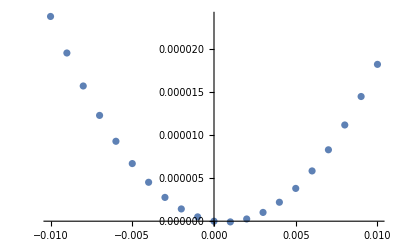

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->.1,f2v->0,pv->0,rv->0,k11->0,k12->f2v};
ListPlot[Table[{f2v,(Fit[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,50}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->500})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->0})))/500},{Jxv1,0.1,0.9,.1}],{1,x},x])/.{x->0}},{f2v,-.01,.01,0.001}]]
```

{Jx'[t]==0.000075 Jx[t] Jy[t] (0.0002 Cos[0.4 t+2 ϕx[t]-2 ϕy[t]]-2 Sin[0.4 t+2 ϕx[t]-2 ϕy[t]])-1/2 (1/2 p Jx[t]^3 √Jy[t]+0.00005 √Jx[t] Jy[t]^3) (0.0001 Cos[0.2 t+ϕx[t]-ϕy[t]]-Sin[0.2 t+ϕx[t]-ϕy[t]]),Jy'[t]==0.000075 Jx[t] Jy[t] (-0.0002 Cos[0.4 t+2 ϕx[t]-2 ϕy[t]]+2 Sin[0.4 t+2 ϕx[t]-2 ϕy[t]])-1/2 (1/2 p Jx[t]^3 √Jy[t]+0.00005 √Jx[t] Jy[t]^3) (-0.0001 Cos[0.2 t+ϕx[t]-ϕy[t]]+Sin[0.2 t+ϕx[t]-ϕy[t]]),ϕx'[t]==3/8 (0.0002 Jx[t]+0.0002 Jy[t])-0.000075 Jy[t] (Cos[0.4 t+2 ϕx[t]-2 ϕy[t]]+0.0001 Sin[0.4 t+2 ϕx[t]-2 ϕy[t]])+1/2 (3/2 p Jx[t]^2 √Jy[t]+(0.000025 Jy[t]^3)/(√Jx[t])) (Cos[0.2 t+ϕx[t]-ϕy[t]]+0.0001 Sin[0.2 t+ϕx[t]-ϕy[t]]),ϕy'[t]==3/8 (0.0002 Jx[t]+0.0002 Jy[t])-0.000075 Jx[t] (Cos[0.4 t+2 ϕx[t]-2 ϕy[t]]+0.0001 Sin[0.4 t+2 ϕx[t]-2 ϕy[t]])+1/2 ((p Jx[t]^3)/(4 √Jy[t])+0.00015 √Jx[t] Jy[t]^2) (Cos[0.2 t+ϕx[t]-ϕy[t]]+0.0001 Sin[0.2 t+ϕx[t]-ϕy[t]]),Jx[0]==Jxv1,Jy[0]==0.1-Jxv1,ϕx[0]==π/2,ϕy[0]==0}

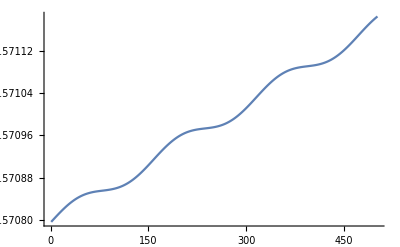
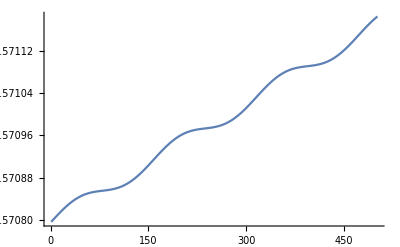
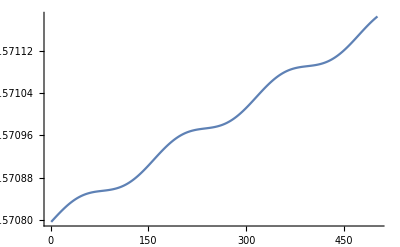
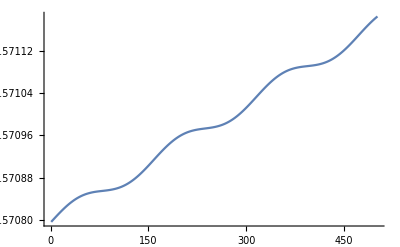
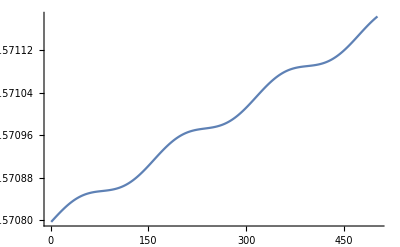

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->.1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.1,f2v->.0001,pv->.0001,rv->.0001,f1v->0,k11->p,k12->.0001,f11->.0001,f21->.0001,q->.0001}
Table[ListPlot[Table[ϕx[t]/.Flatten[NDSolve[inloc/.{p->p,Jxv1->0.02},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]]/.{t->t1},{t1,0,50,.1}],Joined->True],{p,-.001,.001,0.0005}]
```

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.1,f2v->0.01,pv->.2,rv->.1,f1v->0,k11->.05,k12->-.05};
Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,50}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->500})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->0})))/500},{Jxv1,0.1,0.9,.1}]
```

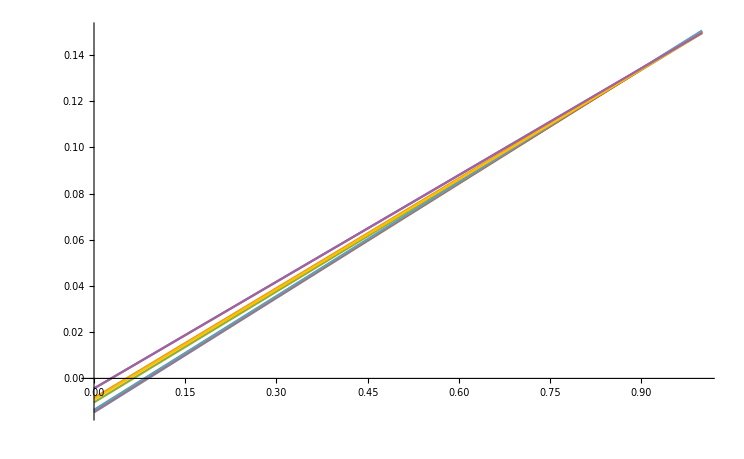

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->.1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.1,f2v->.0001,pv->.0001,rv->.0001,f1v->0,k11->p,k12->.0001};
Table[ListPlot[Table[Sqrt[Jx[t]]/.Flatten[NDSolve[inloc/.{p->p,Jxv1->0.02},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]]/.{t->t1},{t1,0,50,.1}],Joined->True],{p,-.01,.01,0.005}]
```

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->.1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.1,f2v->.0001,pv->.000,rv->.0001,f1v->0,k11->p,k12->.0001};
Manipulate[ListPlot[Table[(ϕx[t] Sqrt[Jx[t]])/.Flatten[NDSolve[inloc/.{p->p1,Jxv1->0.05},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]]/.{t->t1},{t1,0,50,1}],Joined->True],{p1,-.1,.1}]
```

NDSolve::nlnum: The function value {5.07571×10^-7+0.001 Sin[1.57678-0.00511848 wr],-5.07571×10^-7+0.001 Sin[0.00562998-0.00511848 wr],0.007125,0.000375038} is not a list of numbers with dimensions {4} at {t,Jx[t],Jy[t],ϕx[t],ϕy[t]} = {0.00511848,0.0500051,0.95,1.57083,1.91943×10^-6}.

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::nlnum: The function value {5.07571×10^-7+0.001 Sin[1.57678-0.00511848 wr],-5.07571×10^-7+0.001 Sin[0.00562998-0.00511848 wr],0.007125,0.000375038} is not a list of numbers with dimensions {4} at {t,Jx[t],Jy[t],ϕx[t],ϕy[t]} = {0.00511848,0.0500051,0.95,1.57083,1.91943×10^-6}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::mxst: Maximum number of 115003 steps reached at the point t == 0.00110723.

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {1} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {1} and/or the interpolation grid is insufficient to compute the value.

NDSolve::mxst: Maximum number of 115003 steps reached at the point t == 0.00110723.

General::stop: Further output of NDSolve::mxst will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dprec: The precision of input value {2} and/or the interpolation grid is insufficient to compute the value.

General::stop: Further output of InterpolatingFunction::dprec will be suppressed during this calculation.

NDSolve::mxst: Maximum number of 115003 steps reached at the point t == 6.03883×10^-6.